```mathematica
zero={{0,0},{0,0}};
```

```mathematica
Σ=ArrayFlatten[{{ⅈ PauliMatrix[2],zero},{zero,ⅈ PauliMatrix[2]}}];
```

(A | Cc
Cc | B)

```mathematica
s=Table[RandomReal[{1,100}],{i,10^3}];
d=Table[RandomReal[{0,s[[i]]-1}],{i,10^3}];
g=Table[RandomReal[{2 Abs[d[[i]]]+1,2s[[i]]-1}],{i,10^3}];
λ=Table[RandomReal[{-1,1}],{i,10^3}];

a=Table[s[[i]]+d[[i]],{i,10^3}];

b=Table[s[[i]]-d[[i]],{i,10^3}];


cp=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)+√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^3}]//FullSimplify;

cm=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)-√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^3}]//FullSimplify;
```

```mathematica
cp[[1]]
```

1.84384

```mathematica
covm=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,cm[[i]]},{cp[[i]],0,b[[i]],0},{0,cm[[i]],0,b[[i]]}},{i,10^3}];
```

```mathematica
covm[[4]]
```

{{155.853,0,72.2925,0},{0,155.853,0,1.8407},{72.2925,0,33.5747,0},{0,1.8407,0,33.5747}}

{{9.05891,0,-1.80664,0},{0,9.05891,0,-3.84297},{-1.80664,0,5.39379,0},{0,-3.84297,0,5.39379}}

```mathematica
Clear[phystest]
```

```mathematica
phystest={};
Do[AppendTo[phystest,{Eigenvalues[covm[[i]]],Eigenvalues[covm[[i]]+ⅈ Σ],Abs[Eigenvalues[ⅈ Σ . covm[[i]]//Chop]]}];,{i,1,Length[covm]}]
```

```mathematica
Length[phystest]
```

1000

```mathematica
phystest[[200]]
```

{{11.3882,10.8468,1.2748,0.733424},{12.1016,10.1589,1.96265,0.0199488},{10.5183,10.5183,1.02172,1.02172}}

```mathematica
{1,Min[phystest[[1,1]]]}
```

-60.9954

```mathematica
Table[{i,Min[phystest[[i,1]]]},{i,1,Length[cm]}]
```

{{1,0.892087},{2,0.915505},{3,0.108856},{4,0.265778},{5,0.767489},{6,0.245187},{7,0.913582},{8,0.111845},{9,0.173474},{10,0.249152},{11,0.142701},{12,0.967573},{13,0.172265},{14,0.356659},{15,0.167906},{16,0.383553},{17,0.261836},{18,0.248463},{19,0.256123},{20,0.456825},{21,0.298994},{22,0.505991},{23,0.170992},{24,0.605231},{25,0.259563},{26,0.114854},{27,0.415489},{28,0.52235},{29,0.851833},{30,0.351929},{31,0.188205},{32,0.534234},{33,0.317258},{34,0.460267},{35,0.719536},{36,0.661743},{37,0.265586},{38,0.495814},{39,0.191811},{40,0.13031},{41,0.230258},{42,0.406022},{43,0.294744},{44,0.943466},{45,0.683682},{46,0.411718},{47,0.321858},{48,0.0650346},{49,0.365907},{50,0.372618},{51,0.935108},{52,0.3939},{53,0.453152},{54,0.529403},{55,0.246093},{56,0.114747},{57,0.19439},{58,0.193529},{59,0.316372},{60,0.935061},{61,0.272136},{62,0.70361},{63,0.175861},{64,0.485951},{65,0.789039},{66,0.097155},{67,0.392164},{68,0.791303},{69,0.643897},{70,0.326067},{71,0.100721},{72,0.28436},{73,0.686623},{74,0.549878},{75,0.281096},{76,0.831239},{77,0.268452},{78,0.761641},{79,0.320237},{80,0.226452},{81,0.828294},{82,0.299689},{83,0.261439},{84,0.976957},{85,0.441234},{86,0.692522},{87,0.596706},{88,0.175297},{89,0.371289},{90,0.333905},{91,0.1961},{92,0.322879},{93,0.501657},{94,0.28314},{95,0.17965},{96,0.720025},{97,0.329477},{98,0.370499},{99,0.117572},{100,0.918957},{101,0.999538},{102,0.422697},{103,0.441879},{104,0.435858},{105,0.135558},{106,0.431474},{107,0.227744},{108,0.136462},{109,0.655813},{110,0.357984},{111,0.532936},{112,0.0893613},{113,0.67973},{114,0.776708},{115,0.350032},{116,0.863189},{117,0.280406},{118,0.344589},{119,0.414336},{120,0.8134},{121,0.417769},{122,0.926298},{123,0.46954},{124,0.100811},{125,0.623317},{126,0.654632},{127,0.415641},{128,0.585449},{129,0.612349},{130,0.882803},{131,0.747557},{132,0.180186},{133,0.66114},{134,0.370389},{135,0.265728},{136,0.203241},{137,0.106446},{138,0.325694},{139,0.551962},{140,0.493296},{141,0.79271},{142,0.495979},{143,0.4456},{144,0.419664},{145,0.823866},{146,0.678075},{147,0.826895},{148,0.86563},{149,0.271304},{150,0.168763},{151,0.554932},{152,0.49153},{153,0.717469},{154,0.188741},{155,0.874923},{156,0.293917},{157,0.157976},{158,0.854647},{159,0.111425},{160,0.17701},{161,0.522232},{162,0.274004},{163,0.441944},{164,0.962743},{165,0.909023},{166,0.339149},{167,0.134443},{168,0.223016},{169,0.538353},{170,0.582697},{171,0.523262},{172,0.305704},{173,0.385565},{174,0.0980966},{175,0.326021},{176,0.530384},{177,0.229},{178,0.516441},{179,0.427167},{180,0.545865},{181,0.683727},{182,0.216718},{183,0.793681},{184,0.130093},{185,0.223581},{186,0.611266},{187,0.790009},{188,0.728261},{189,0.17081},{190,0.583803},{191,0.14268},{192,0.556882},{193,0.467503},{194,0.236268},{195,0.248088},{196,0.147619},{197,0.407577},{198,0.686},{199,0.48064},{200,0.733424},{201,0.702416},{202,0.522934},{203,0.638783},{204,0.173579},{205,0.944042},{206,0.500136},{207,0.409525},{208,0.198636},{209,0.60991},{210,0.119602},{211,0.267204},{212,0.474007},{213,0.915463},{214,0.205777},{215,0.63295},{216,0.425667},{217,0.595683},{218,0.50878},{219,0.459605},{220,0.111226},{221,0.24425},{222,0.734049},{223,0.231187},{224,0.865124},{225,0.210602},{226,0.247884},{227,0.553343},{228,0.95809},{229,0.197236},{230,0.680938},{231,0.959725},{232,0.990358},{233,0.76947},{234,0.083119},{235,0.635588},{236,0.26609},{237,0.275378},{238,0.570012},{239,0.6457},{240,0.750363},{241,0.244358},{242,0.260637},{243,0.670178},{244,0.355302},{245,0.22161},{246,0.152682},{247,0.259585},{248,0.791655},{249,0.268968},{250,0.250739},{251,0.994379},{252,0.135702},{253,0.890228},{254,0.182197},{255,0.57543},{256,0.226363},{257,0.24072},{258,0.241976},{259,0.187109},{260,0.399809},{261,0.149598},{262,0.305401},{263,0.593881},{264,0.193733},{265,0.485759},{266,0.45408},{267,0.555519},{268,0.291505},{269,0.366354},{270,0.24287},{271,0.923026},{272,0.347304},{273,0.502302},{274,0.226333},{275,0.218239},{276,0.378257},{277,0.542671},{278,0.201377},{279,0.688951},{280,0.290885},{281,0.561353},{282,0.793134},{283,0.221899},{284,0.950187},{285,0.0687457},{286,0.656959},{287,0.334516},{288,0.127164},{289,0.829207},{290,0.18191},{291,0.685926},{292,0.137319},{293,0.331016},{294,0.220891},{295,0.394695},{296,0.744999},{297,0.135279},{298,0.692994},{299,0.742744},{300,0.725572},{301,0.14927},{302,0.535754},{303,0.328486},{304,0.317098},{305,0.515731},{306,0.649377},{307,0.858402},{308,0.093214},{309,0.216607},{310,0.318724},{311,0.850731},{312,0.306859},{313,0.153675},{314,0.187456},{315,0.849662},{316,0.987088},{317,0.303993},{318,0.353173},{319,0.209898},{320,0.47156},{321,0.370182},{322,0.46659},{323,0.118009},{324,0.158267},{325,0.0905628},{326,0.30492},{327,0.882473},{328,0.16349},{329,0.382141},{330,0.362384},{331,0.993201},{332,0.233955},{333,0.641044},{334,0.593879},{335,0.418836},{336,0.715294},{337,0.558447},{338,0.297779},{339,0.585334},{340,0.483369},{341,0.225266},{342,0.149084},{343,0.178733},{344,0.815457},{345,0.255399},{346,0.50154},{347,0.204429},{348,0.254674},{349,0.306383},{350,0.72415},{351,0.202888},{352,0.287142},{353,0.256067},{354,0.435946},{355,0.730946},{356,0.21769},{357,0.407043},{358,0.369962},{359,0.14823},{360,0.412923},{361,0.519765},{362,0.327381},{363,0.0853584},{364,0.514758},{365,0.643262},{366,0.377537},{367,0.714276},{368,0.708614},{369,0.649237},{370,0.538055},{371,0.708763},{372,0.530584},{373,0.66281},{374,0.812433},{375,0.290101},{376,0.42178},{377,0.504652},{378,0.160838},{379,0.610061},{380,0.959601},{381,0.272568},{382,0.976213},{383,0.79206},{384,0.575915},{385,0.632706},{386,0.398569},{387,0.420082},{388,0.668639},{389,0.654279},{390,0.237703},{391,0.675006},{392,0.188786},{393,0.528052},{394,0.509615},{395,0.238215},{396,0.716862},{397,0.91496},{398,0.585061},{399,0.268963},{400,0.593299},{401,0.62156},{402,0.134739},{403,0.919983},{404,0.77025},{405,0.297385},{406,0.151845},{407,0.894195},{408,0.689183},{409,0.301575},{410,0.933348},{411,0.907457},{412,0.750753},{413,0.810947},{414,0.737366},{415,0.695277},{416,0.461251},{417,0.309785},{418,0.538903},{419,0.643866},{420,0.348217},{421,0.665007},{422,0.489948},{423,0.870677},{424,0.490176},{425,0.358958},{426,0.492095},{427,0.533277},{428,0.156513},{429,0.22904},{430,0.593313},{431,0.719062},{432,0.724369},{433,0.38525},{434,0.284205},{435,0.295387},{436,0.318879},{437,0.452557},{438,0.0872927},{439,0.395703},{440,0.140639},{441,0.358276},{442,0.259242},{443,0.240895},{444,0.675078},{445,0.871739},{446,0.786167},{447,0.383837},{448,0.0630131},{449,0.132363},{450,0.261882},{451,0.924671},{452,0.427756},{453,0.457566},{454,0.235119},{455,0.40482},{456,0.999542},{457,0.251032},{458,0.324038},{459,0.301844},{460,0.724306},{461,0.232163},{462,0.411649},{463,0.329733},{464,0.223444},{465,0.108273},{466,0.276069},{467,0.510394},{468,0.179239},{469,0.851272},{470,0.60775},{471,0.159185},{472,0.486686},{473,0.720624},{474,0.17657},{475,0.878125},{476,0.50429},{477,0.255942},{478,0.590141},{479,0.539389},{480,0.229216},{481,0.600865},{482,0.287182},{483,0.454215},{484,0.823981},{485,0.482112},{486,0.433381},{487,0.794948},{488,0.750778},{489,0.369937},{490,0.424689},{491,0.812602},{492,0.563212},{493,0.356964},{494,0.572825},{495,0.98533},{496,0.916949},{497,0.49146},{498,0.539514},{499,0.355294},{500,0.82894},{501,0.9189},{502,0.202187},{503,0.915199},{504,0.281431},{505,0.870748},{506,0.140747},{507,0.16515},{508,0.530032},{509,0.511438},{510,0.822509},{511,0.676285},{512,0.800321},{513,0.255652},{514,0.277486},{515,0.390731},{516,0.134768},{517,0.15753},{518,0.314163},{519,0.322444},{520,0.250887},{521,0.264545},{522,0.122861},{523,0.19502},{524,0.922987},{525,0.644097},{526,0.899052},{527,0.964938},{528,0.7651},{529,0.786246},{530,0.513727},{531,0.366055},{532,0.149667},{533,0.553768},{534,0.299704},{535,0.368868},{536,0.59869},{537,0.928293},{538,0.635127},{539,0.632954},{540,0.418411},{541,0.415932},{542,0.853539},{543,0.790674},{544,0.462339},{545,0.282417},{546,0.212822},{547,0.163951},{548,0.352061},{549,0.343768},{550,0.802227},{551,0.165026},{552,0.37113},{553,0.326083},{554,0.178893},{555,0.686768},{556,0.193282},{557,0.890349},{558,0.226431},{559,0.244535},{560,0.278381},{561,0.568083},{562,0.590875},{563,0.660937},{564,0.234254},{565,0.689202},{566,0.673036},{567,0.101891},{568,0.885189},{569,0.236359},{570,0.406014},{571,0.197116},{572,0.353235},{573,0.141486},{574,0.972288},{575,0.106557},{576,0.445127},{577,0.589944},{578,0.809169},{579,0.09427},{580,0.90403},{581,0.130748},{582,0.43593},{583,0.428505},{584,0.261489},{585,0.641303},{586,0.869577},{587,0.705454},{588,0.271853},{589,0.195964},{590,0.418553},{591,0.473708},{592,0.288812},{593,0.443692},{594,0.538839},{595,0.35161},{596,0.354188},{597,0.20687},{598,0.374521},{599,0.559545},{600,0.931679},{601,0.232514},{602,0.13533},{603,0.457118},{604,0.45946},{605,0.349941},{606,0.408449},{607,0.79445},{608,0.709142},{609,0.763606},{610,0.717423},{611,0.405062},{612,0.210965},{613,0.247502},{614,0.24185},{615,0.176545},{616,0.455605},{617,0.477683},{618,0.62202},{619,0.613394},{620,0.447207},{621,0.401598},{622,0.84695},{623,0.907403},{624,0.427752},{625,0.603072},{626,0.588817},{627,0.319665},{628,0.669444},{629,0.673049},{630,0.749104},{631,0.369992},{632,0.293024},{633,0.192934},{634,0.160797},{635,0.913676},{636,0.488923},{637,0.703758},{638,0.990673},{639,0.42582},{640,0.432688},{641,0.415608},{642,0.706417},{643,0.492747},{644,0.148568},{645,0.457719},{646,0.431163},{647,0.916043},{648,0.935277},{649,0.522022},{650,0.392786},{651,0.60705},{652,0.333849},{653,0.595937},{654,0.498737},{655,0.812256},{656,0.518798},{657,0.235295},{658,0.684415},{659,0.961946},{660,0.557287},{661,0.241644},{662,0.276812},{663,0.516336},{664,0.429233},{665,0.449803},{666,0.889039},{667,0.120676},{668,0.617081},{669,0.468681},{670,0.242278},{671,0.661301},{672,0.479467},{673,0.476338},{674,0.462052},{675,0.300566},{676,0.66246},{677,0.091683},{678,0.308566},{679,0.259508},{680,0.331835},{681,0.60757},{682,0.704734},{683,0.220925},{684,0.733279},{685,0.385891},{686,0.10263},{687,0.993706},{688,0.124335},{689,0.514312},{690,0.559503},{691,0.75092},{692,0.7111},{693,0.121629},{694,0.358407},{695,0.867154},{696,0.353163},{697,0.779692},{698,0.791351},{699,0.197605},{700,0.494615},{701,0.280117},{702,0.313355},{703,0.574733},{704,0.686704},{705,0.788297},{706,0.126444},{707,0.677346},{708,0.182408},{709,0.371766},{710,0.664196},{711,0.0939554},{712,0.242689},{713,0.186937},{714,0.283269},{715,0.561139},{716,0.509143},{717,0.826531},{718,0.556096},{719,0.678906},{720,0.19999},{721,0.886149},{722,0.529082},{723,0.152765},{724,0.167009},{725,0.37377},{726,0.303229},{727,0.978688},{728,0.770945},{729,0.694807},{730,0.110698},{731,0.649858},{732,0.667454},{733,0.281555},{734,0.982252},{735,0.159424},{736,0.878236},{737,0.328182},{738,0.475622},{739,0.248436},{740,0.153096},{741,0.608156},{742,0.714661},{743,0.657778},{744,0.150417},{745,0.12634},{746,0.947238},{747,0.179875},{748,0.496118},{749,0.240595},{750,0.598616},{751,0.814306},{752,0.935957},{753,0.409189},{754,0.496607},{755,0.221357},{756,0.823631},{757,0.44509},{758,0.32146},{759,0.0982062},{760,0.608364},{761,0.53447},{762,0.223752},{763,0.315336},{764,0.331614},{765,0.33022},{766,0.17669},{767,0.827093},{768,0.448197},{769,0.939088},{770,0.39544},{771,0.755745},{772,0.771327},{773,0.0802941},{774,0.375408},{775,0.592038},{776,0.868235},{777,0.325988},{778,0.733708},{779,0.713553},{780,0.467683},{781,0.636697},{782,0.14431},{783,0.549692},{784,0.578641},{785,0.897002},{786,0.285264},{787,0.935293},{788,0.0885981},{789,0.363185},{790,0.352407},{791,0.260725},{792,0.709651},{793,0.252416},{794,0.866043},{795,0.64728},{796,0.224246},{797,0.654261},{798,0.152509},{799,0.277381},{800,0.184198},{801,0.902565},{802,0.12811},{803,0.1264},{804,0.714043},{805,0.400399},{806,0.7758},{807,0.190701},{808,0.142395},{809,0.286176},{810,0.159336},{811,0.201733},{812,0.871763},{813,0.15708},{814,0.736702},{815,0.101726},{816,0.2605},{817,0.69935},{818,0.288857},{819,0.392059},{820,0.468226},{821,0.620858},{822,0.524478},{823,0.142206},{824,0.393982},{825,0.29807},{826,0.733708},{827,0.429308},{828,0.0946509},{829,0.377456},{830,0.404769},{831,0.438465},{832,0.410769},{833,0.718529},{834,0.224685},{835,0.90052},{836,0.377742},{837,0.311191},{838,0.358546},{839,0.758638},{840,0.193627},{841,0.186441},{842,0.296482},{843,0.617634},{844,0.251873},{845,0.109184},{846,0.338773},{847,0.483875},{848,0.28893},{849,0.230616},{850,0.428779},{851,0.2089},{852,0.511897},{853,0.163984},{854,0.196252},{855,0.174165},{856,0.216989},{857,0.465135},{858,0.273734},{859,0.797801},{860,0.269375},{861,0.452502},{862,0.454461},{863,0.123132},{864,0.438023},{865,0.460118},{866,0.518338},{867,0.680253},{868,0.459598},{869,0.534796},{870,0.846042},{871,0.0980116},{872,0.253257},{873,0.574265},{874,0.774064},{875,0.355877},{876,0.351614},{877,0.494415},{878,0.254524},{879,0.571677},{880,0.592003},{881,0.936217},{882,0.250325},{883,0.605043},{884,0.766506},{885,0.972659},{886,0.339671},{887,0.71922},{888,0.155047},{889,0.69135},{890,0.159664},{891,0.32198},{892,0.284535},{893,0.619033},{894,0.398417},{895,0.460875},{896,0.429524},{897,0.62782},{898,0.889326},{899,0.187769},{900,0.769049},{901,0.466044},{902,0.750145},{903,0.289358},{904,0.417731},{905,0.138319},{906,0.835307},{907,0.821252},{908,0.294014},{909,0.275086},{910,0.422504},{911,0.0905452},{912,0.577184},{913,0.287764},{914,0.560464},{915,0.3977},{916,0.950138},{917,0.605263},{918,0.567804},{919,0.811243},{920,0.163749},{921,0.230256},{922,0.123085},{923,0.508767},{924,0.858123},{925,0.870889},{926,0.68271},{927,0.286447},{928,0.314054},{929,0.627226},{930,0.108547},{931,0.814403},{932,0.29101},{933,0.105872},{934,0.417947},{935,0.643244},{936,0.84251},{937,0.133423},{938,0.796249},{939,0.623468},{940,0.84615},{941,0.612096},{942,0.203308},{943,0.267418},{944,0.773224},{945,0.145794},{946,0.226266},{947,0.275729},{948,0.207642},{949,0.192651},{950,0.943608},{951,0.641227},{952,0.235115},{953,0.486677},{954,0.0783674},{955,0.858306},{956,0.0758236},{957,0.57648},{958,0.224924},{959,0.120427},{960,0.11359},{961,0.767878},{962,0.493559},{963,0.0972152},{964,0.15099},{965,0.679127},{966,0.519943},{967,0.388958},{968,0.968647},{969,0.788456},{970,0.42225},{971,0.307449},{972,0.494739},{973,0.921261},{974,0.404303},{975,0.670618},{976,0.505342},{977,0.409616},{978,0.214222},{979,0.339341},{980,0.857685},{981,0.412357},{982,0.293455},{983,0.847746},{984,0.465592},{985,0.447414},{986,0.19141},{987,0.501931},{988,0.967885},{989,0.837561},{990,0.302613},{991,0.634513},{992,0.39226},{993,0.768613},{994,0.407406},{995,0.0667236},{996,0.638674},{997,0.998037},{998,0.707733},{999,0.865567},{1000,0.560933}}

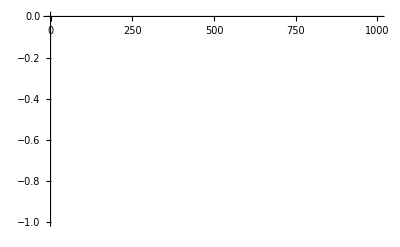

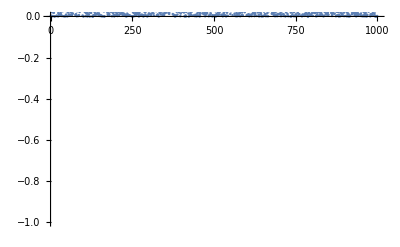

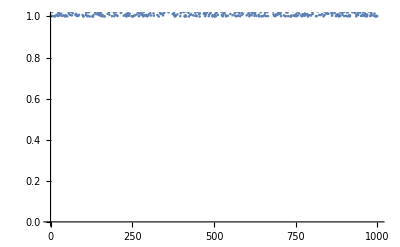

```mathematica
ListPlot[Table[{i,Min[phystest[[i,1]]]},{i,1,Length[cm]}],PlotRange->{-1,0}]
ListPlot[Table[{i,Min[phystest[[i,2]]]},{i,1,Length[cm]}],PlotRange->{-1,0}]
ListPlot[Table[{i,Min[phystest[[i,3]]]},{i,1,Length[cm]}],PlotRange->{0,1}]
```

```mathematica
Clear[cm]
```

```mathematica
Eigenvalues[σ[a,b,cp,cm]]//FullSimplify
```

{1/2 (a+b-√((a-b)^2+4 cm^2)),1/2 (a+b+√((a-b)^2+4 cm^2)),1/2 (a+b-√((a-b)^2+4 cp^2)),1/2 (a+b+√((a-b)^2+4 cp^2))}

```mathematica
Eigenvalues[σ[a,b,cp,cm]+ⅈ Σ]//FullSimplify
```

{1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2))))}

```mathematica
Eigenvalues[ⅈ Σ . σ[a,b,cp,cm]]//FullSimplify
```

{-(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),-(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2)}